```mathematica
parseRow[r_]:=If[StringMatchQ[#, NumberString],#//ToExpression,#]&/@StringSplit[r[[1]],"\t"]
```

```mathematica
cols={"GLOBALEVENTID","SQLDATE","MonthYear","Year","FractionDate","Actor1Code","Actor1Name","Actor1CountryCode","Actor1KnownGroupCode","Actor1EthnicCode","Actor1Religion1Code","Actor1Religion2Code","Actor1Type1Code","Actor1Type2Code","Actor1Type3Code","Actor2Code","Actor2Name","Actor2CountryCode","Actor2KnownGroupCode","Actor2EthnicCode","Actor2Religion1Code","Actor2Religion2Code","Actor2Type1Code","Actor2Type2Code","Actor2Type3Code","IsRootEvent","EventCode","EventBaseCode","EventRootCode","QuadClass","GoldsteinScale","NumMentions","NumSources","NumArticles","AvgTone","Actor1Geo_Type","Actor1Geo_FullName","Actor1Geo_CountryCode","Actor1Geo_ADM1Code","Actor1Geo_Lat","Actor1Geo_Long","Actor1Geo_FeatureID","Actor2Geo_Type","Actor2Geo_FullName","Actor2Geo_CountryCode","Actor2Geo_ADM1Code","Actor2Geo_Lat","Actor2Geo_Long","Actor2Geo_FeatureID","ActionGeo_Type","ActionGeo_FullName","ActionGeo_CountryCode","ActionGeo_ADM1Code","ActionGeo_Lat","ActionGeo_Long","ActionGeo_FeatureID","DATEADDED", "URL"};
```

```mathematica
csv=parseRow/@Import[NotebookDirectory[]<>"random-sample-20130401-20150731.csv"];
```

```mathematica
Extract[#,List/@Flatten[Position[cols,#]&/@{ "EventCode", "Actor1CountryCode"}]]&/@RandomChoice[Select[csv,Length[#]≥57&], 10]
```

{{36,},{57,},{42,},{173,},{40,GUY},{50,},{311,},{51,SYR},{36,BHS},{51,}}

```mathematica
(* Drop the first item, the empty string*)
actors1={First@First@#,Length@DeleteDuplicates[Last/@#]}&/@SplitBy[Sort[csv[[All,{7,17}]]],First]//Rest;
actors2={First@First@#,Length@DeleteDuplicates[Last/@#]}&/@SplitBy[Sort[csv[[All,{17,7}]]],First]//Rest;
```

```mathematica
n5Sum[x_]:={Text/@{"Min", "Q1", "Med", "Q3", "Max"}, {Min@x}~Join~Quartiles[x]~Join~{Max@x}}
```

```mathematica
Grid[
{Text/@{"# A2 by A1", "# A1 by A2"},{Grid[n5Sum[Last/@actors1]],Grid[n5Sum[Last/@actors2]]}},Frame->All]
```

# A2 by A1 | # A1 by A2
Min | Q1 | Med | Q3 | Max
1 | 1 | 3 | 9 | 988 | Min | Q1 | Med | Q3 | Max
1 | 1 | 3 | 10 | 990

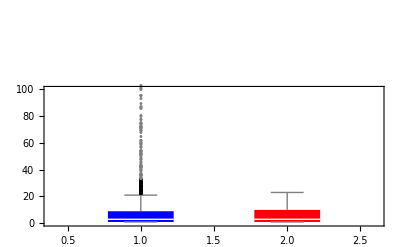

```mathematica
BoxWhiskerChart[{Last/@actors1,Last/@ actors2},"Outliers",ChartStyle->{Blue,Red},ChartLabels->{"Actor2 per Actor1", "Actor1 per Actor2"}, PlotRange->{0, 100}]
```

```mathematica
SortBy[actors1, Last][[-5;;]]
SortBy[actors2, Last][[-5;;]]
```

{{PRESIDENT,427},{GOVERNMENT,443},{POLICE,492},{UNITED STATES,988},{,1560}}

{{PRESIDENT,393},{POLICE,409},{GOVERNMENT,521},{UNITED STATES,990},{,2341}}

```mathematica
Length[csv]
```

123750

```mathematica
actors1[[First@First@Position[nActorsByActor1,Max[nActorsByActor1]]]]
```

UNITED STATES

```mathematica
actors2[[First@First@Position[nActorsByActor2,Max[nActorsByActor2]]]]
```

UNITED STATES

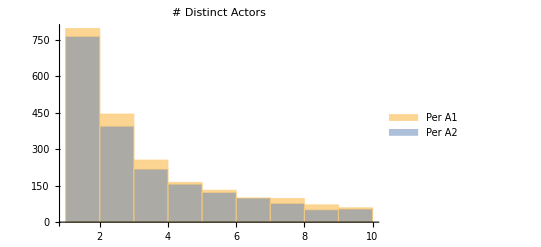

```mathematica
infreqBit1=nActorsByActor1<10//Thread;
infreqBit2=nActorsByActor2<10//Thread;
Histogram[{Pick[nActorsByActor1,infreqBit1],Pick[nActorsByActor2,infreqBit2] }, ChartLegends->{"Per A1", "Per A2"}, PlotLabel->"# Distinct Actors"]
```

```mathematica
infreqA1s=Pick[actors1,infreqBit1];
infreqA2s=Pick[actors2,infreqBit2];
Length@Intersection[infreqA1s,infreqA2s]/Length@Union[infreqA1s,infreqA2s]//N
```

0.609785

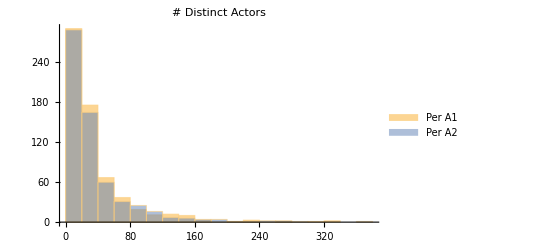

```mathematica
freqBit1=10≤nActorsByActor1<400// Thread;
freqBit2=10≤nActorsByActor2<400//Thread;
Histogram[{Pick[nActorsByActor1,freqBit1],Pick[nActorsByActor2,freqBit2] }, ChartLegends->{"Per A1", "Per A2"}, PlotLabel->"# Distinct Actors"]
```

```mathematica
BoxWhiskerChart[{nActorsByActor1, nActorsByActor2},"Outliers",ChartStyle->50,ChartLegends->{"# Actors 2 per Actor 1", "# Actors 1 per Actor 2"}]
```

```mathematica
Position[cols,"EventBaseCode"]
```

{{28}}

```mathematica
(* Drop the first item, the empty string*)
events1={First@First@#,Length@#}&/@SplitBy[Sort[csv[[All,{7,28}]]],First]//Rest;
events2={First@First@#,Length@#}&/@SplitBy[Sort[csv[[All,{17,28}]]],First]//Rest;
```

```mathematica
n5Sum/@{Last/@events1, Last/@events2}//TableForm
```

Min
Q1
Med
Q3
Max | 1
1
3
14
11905
Min
Q1
Med
Q3
Max | 1
1
3
12
8809

```mathematica
Remove[less]
```

```mathematica
less[q_][x_]:=Select[x, #<Quantile[x,q]&]
```

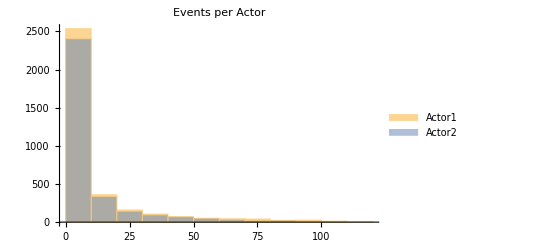

```mathematica
Histogram[less[.95]/@{Last/@events1, Last/@events2},ChartLegends->{"Actor1", "Actor2"}, PlotLabel->"Events per Actor" ]
```

```mathematica
(* TODO: feed in geographic location of the city *)
(* TODO: categorize *)
```